# Model of hierarchical and simultaneous uptake of glycerol with other carbon substrates

## Intro

We here show numerical calculations for the basic modeling results presented in Okano et al, Nature Microbiology (2019). The mathematical details are described in the Supplementary Discussion published with that article. The names of variables below correspond to the notation used in the Supplementary Discussion. d_0

## Model definitions

### Metabolic feedback

FBP inhibition as a function of jL is a decreasing Hill function:

```mathematica
h[jL_, j05_, h0_, m_] := h0/(1 + (jL/j05)^m);
```

### Transcriptional regulation

The effect of snG3P on glpD and glpK expression (via GlpR repression) is assumed to be an increasing Hill function.  For simplicity, no leaky / basal expression is included. In the code below, s stands for the snG3P pool.

```mathematica
gD[s_, kD_, nD_]:= (s^nD)/(kD^nD + s^nD);
gK[s_, kK_, nK_]:= (s^nK)/(kK^nK + s^nK);
```

The effect of CRP on glpK expression is approximately a linear function of growth rate λ (C-line):

```mathematica
fK[λ_, λC_] := λC - λ;
```

To describe the effect of CRP on glpD we using a heuristic function that fits the data well:

```mathematica
fD[λ_, Δv_, sv_, sh_, Δh_]:= If[
λ>Δh, 
Δv, 
sv (Sqrt[1+(sh(λ-Δh))^2]-1)+Δv 
];
```

### Fluxes:

Given the above regulatory functions, the fluxes supported by GlpK and GlpD become:

```mathematica
jK[νK_,jL_,j05_,h0_, s_, kK_, nK_, λ_, λC_, m_]:= SetPrecision[Max[
Re[νK h[jL, j05, h0, m]gK[s,kK, nK]fK[λ, λC]],
0
], 50];
jD[αD_,s_, kD_, nD_, λ_, Δv_, sv_, sh_, Δh_]:= SetPrecision[Max[
Re[αD s gD[s,kD, nD]fD[λ, Δv, sv, sh, Δh]],
0
],50];
```

### Relation between growth rate and total flux:

We assume a linear relation between growth rate and total carbon flux; coefficients a and b are taken from a regression line obtained from measured data.

```mathematica
jTot[a_,b_,λ_]:=aλ-b;
λF[a_, b_, jGA_, jLA_]:= SetPrecision[(jGA + jLA + b)/a,30];
```

## Parameters

### Basic parameters

```mathematica
λC =  1;
a =  42.5;
b =6;
νK =120;
αD = .8;
nK=2;
nD = 1.2;
m = 2;
j05 = 16;
kK=.9/αD;
kD= .6/αD;
h0=0.6;

sv = 4.25;
sh = 5;
Δv = 5.18;
Δh = 0.84;
```

## Calculations

We find the values of jG and s that obey the steady-state requirements that jK = jD and jK = jG by numerical minimization the the function f = (jK-jD)^2 + (jK-jG)^2. The arguments jGInit and sInit are the starting points of the minimization algorithm. The function returns, for given lactose flux jL and parameters, a list with replacement rules for s, jG, and λ.

Because the solution to the equations is found my minimization, one should always check whether the solution is found by checking that the value of f is numerically near zero.  For simplicity, the code below does not perform this check, but it is easy to implement.

```mathematica
solveSystemP[jL_, j05A_, kKA_, kDA_, nKA_,nDA_, h0A_, νKA_, mA_,jGInit_, sInit_]:= Module[{sol, sol2, f},(
sol =FindMinimum[
{
(jK[νKA,jL, j05A, h0A, s, kKA, nKA,λF[a, b, jG, jL], λC, mA] -jD[αD,s, kDA, nDA,λF[a, b, jG, jL], Δv, sv, sh, Δh])^2 + 
(jK[νKA,jL, j05A, h0A, s, kKA, nKA,λF[a, b, jG, jL], λC, mA]-jG)^2,
s>0,jG>0, jG<30
}, 
{{jG,jGInit}, {s, sInit}}, 
Method->"Automatic", 
WorkingPrecision->50,
PrecisionGoal->10, 
AccuracyGoal->10
];
sol2 = sol[[2]];
f = sol[[1]];
If[f> 10^-6 , Print["Warning! f does not vanish at the minimum."]]; (* uncomment this line to print the value of F *)
Append[sol2,λ->  λF[a, b, jG/.sol2, jL]]
)]
```

In the absence of glycerol, the same calculation is much simplified because jG = 0; it is sufficient to minimize f = jD^2 with the following function:

```mathematica
solveSystemPNG[jL_, j05A_, kKA_, kDA_, nKA_,nDA_, h0A_, νKA_,sInit_]:= Module[{sol, sol2, f},(
sol =FindMinimum[
{
(jD[αD,s, kDA, nDA,λF[a, b, 0, jL], Δv, sv, sh, Δh])^2 ,
s>0
}, 
{s, sInit}, 
Method->"Automatic", 
WorkingPrecision->50,
PrecisionGoal->10, 
AccuracyGoal->10
];
sol2 = sol[[2]];
f = sol[[1]];
If[f> 10^-6 , Print["Warning! f does not vanish at the minimum."]];
Flatten[Append[sol2, {λ-> λF[a, b,0, jL], jG->0}]]
)]
```

The following function generates a table for the flux relation by solving the system for a series of values of the lactose flux.

```mathematica
MakeTableFluxFlux[jLmin_, jLmax_, jLinc_, j05A_, kKA_, kDA_, nKA_,nDA_, h0A_, νKA_, mA_, jG0A_, sIA_] := Module[{j, nrpoints, tab,ms,mjG,i, sol},
(
nrpoints = Floor[(jLmax - jLmin)/jLinc]+1;
tab = Table[{0,0},{i, 1, nrpoints}]; 
ms = sIA;
mjG = jG0A;
i = 1;
For[j = jLmin, j≤jLmax, j = j + jLinc,
(
sol = solveSystemP[j, j05A, kKA, kDA, nKA,nDA, h0A, νKA,mA,  mjG, ms];
tab[[i]]={j, jG/.sol};
i++;
mjG = jG/.sol;
ms = s/.sol;
)
];
tab
)
]
```

Similarly, we generate a table of snG3P versus growth rate λ:

```mathematica
MakeTableG3PvsGR[jLmin_, jLmax_, jLinc_, j05A_, kKA_, kDA_, nKA_,nDA_, h0A_, νKA_, mA_, jG0A_, sIA_] := Module[{j, nrpoints, tab,ms,mjG,i,sol},
(
nrpoints = Floor[(jLmax - jLmin)/jLinc]+1;
tab = Table[{0,0},{i, 1, nrpoints}]; 
ms = sIA;
mjG = jG0A;
i = 1;
For[j = jLmin, j≤jLmax, j = j + jLinc,
(
sol = solveSystemP[j, j05A, kKA, kDA, nKA,nDA, h0A, νKA,mA, mjG, ms];
tab[[i]]={λ/.sol, s/.sol};
i++;
mjG = jG/.sol;
ms = s/.sol;
)
];
tab
)
]
```

The same, but for growth without glycerol:

```mathematica
MakeTableG3PvsGRNG[jLmin_, jLmax_, jLinc_, j05A_, kKA_, kDA_, nKA_,nDA_, h0A_, νKA_,sIA_] := Module[{j, nrpoints, tab,ms,mjG,i,sol},
(
nrpoints = Floor[(jLmax - jLmin)/jLinc]+1;
tab = Table[{0,0},{i, 1, nrpoints}]; 
ms = sIA;
i = 1;
For[j = jLmin, j≤jLmax, j = j + jLinc,
(
sol = solveSystemPNG[j, j05A, kKA, kDA, nKA,nDA, h0A, νKA, ms];
tab[[i]]={λ/.sol, s/.sol};
i++;
ms = s/.sol;
)
];
tab
)
]
```

Now generate a table with glpD expression.

```mathematica
MakeTableGlpDvsGR[jLmin_, jLmax_, jLinc_, j05A_, kKA_, kDA_, nKA_,nDA_, h0A_, νKA_, mA_,jG0A_, sIA_, norm_] := Module[{j, nrpoints, tab,ms,mjG,i,sol},
(
nrpoints = Floor[(jLmax - jLmin)/jLinc]+1;
tab = Table[{0,0},{i, 1, nrpoints}]; 
ms = sIA;
mjG = jG0A;
i = 1;
For[j = jLmin, j≤jLmax, j = j + jLinc,
(
sol = solveSystemP[j, j05A, kKA, kDA, nKA,nDA, h0A, νKA,mA, mjG, ms];
tab[[i]]={ λ/.sol, gD[s/.sol, kDA, nDA]*fD[λ /.sol, Δv, sv, sh, Δh]/norm};
i++;
mjG = jG/.sol;
ms = s/.sol;
)
];
tab
)
]
```

Same, for conditions without glycerol :

```mathematica
MakeTableGlpDvsGRNG[jLmin_, jLmax_, jLinc_, j05A_, kKA_, kDA_, nKA_, nDA_, h0A_, νKA_, jG0A_,sIA_, norm_] := Module[{j, nrpoints, tab, ms, mjG, i, sol},
  (
   nrpoints = Floor[(jLmax - jLmin)/jLinc] + 1;
   tab = Table[{0, 0}, {i, 1, nrpoints}]; 
   ms = sIA;
   mjG = jG0A;
   i = 1;
   For[j = jLmin, j <= jLmax, j = j + jLinc,
    (
     sol = solveSystemPNG[j, j05A, kKA, kDA, nKA, nDA, h0A, νKA, ms];
     tab[[i]] = { λ /. sol, gD[s/.sol, kDA, nDA]*fD[λ /.sol, Δv, sv, sh, Δh]/norm};
     i++;
     mjG = jG /. sol;
     ms = s /. sol;
     )
    ];
   tab
   )
  ]
```

Now generate a table with glpFK expression.

```mathematica
MakeTableGlpKvsGR[jLmin_, jLmax_, jLinc_, j05A_, kKA_, kDA_, nKA_, nDA_, h0A_, νKA_, mA_,jG0A_, sIA_, norm_] := Module[{j, nrpoints, tab, ms, mjG, i, sol},
  (
   nrpoints = Floor[(jLmax - jLmin)/jLinc] + 1;
   tab = Table[{0, 0}, {i, 1, nrpoints}]; 
   ms = sIA;
   mjG = jG0A;
   i = 1;
   For[j = jLmin, j <= jLmax, j = j + jLinc,
    (
     sol = solveSystemP[j, j05A, kKA, kDA, nKA, nDA, h0A, νKA,mA, mjG, ms];
     tab[[i]] = { λ /. sol,gK[s /. sol, kKA, nKA]*fK[λ /. sol, λC]/norm};
     i++;
     mjG = jG /. sol;
     ms = s /. sol;
     )
    ];
   tab
   )
  ]
```

Same, for conditions without glycerol.

```mathematica
MakeTableGlpKvsGRNG[jLmin_, jLmax_, jLinc_, j05A_, kKA_, kDA_, nKA_, nDA_, h0A_, νKA_, jG0A_,sIA_, norm_] := Module[{j, nrpoints, tab, ms, mjG, i, sol},
  (
   nrpoints = Floor[(jLmax - jLmin)/jLinc] + 1;
   tab = Table[{0, 0}, {i, 1, nrpoints}]; 
   ms = sIA;
   mjG = jG0A;
   i = 1;
   For[j = jLmin, j <= jLmax, j = j + jLinc,
    (
     sol = solveSystemPNG[j, j05A, kKA, kDA, nKA, nDA, h0A, νKA, ms];
     tab[[i]] = { λ /. sol,gK[s /. sol, kKA, nKA]*fK[λ /. sol, λC]/norm};
     i++;
     mjG = jG /. sol;
     ms = s /. sol;
     )
    ];
   tab
   )
  ]
```

## Plots

### Shorthands (used for plotting)

The x-intercept of the flux relation of the glpK22 ΔglpR strain:

```mathematica
jmax = N[jTot[ a, b, λC]];
```

The y-intercept of the flux relation of the glpK22 ΔglpR strain:

```mathematica
jGmax = 27;
```

### Flux relations

We plot the flux relation for four strains.

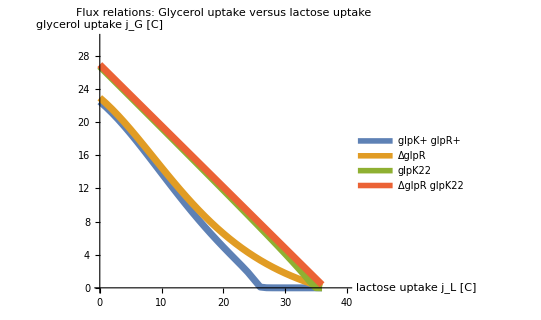

```mathematica
ListPlot[
{
(* glpK glpR+ *)
MakeTableFluxFlux[0, jmax, 1, j05, kK, kD, nK,nD, h0, νK, m,jGmax, 2], 
(* ΔglpR; this is implemented by setting kK and kD to 0 *)
MakeTableFluxFlux[0, jmax, 1, j05, 0, 0, nK,nD, h0, νK, m,jGmax, 2],
(* glpK22; this is implemented by setting j05 to Infinity *)
MakeTableFluxFlux[0, jmax, 1, Infinity, kK, kD, nK,nD, 1, νK, m,jGmax, 2],
(* ΔglpR glpK22; this is implemented by setting kK and kD to 0 and j05 to Infinity *)
MakeTableFluxFlux[0, jmax, 1, Infinity, 0, 0, nK,nD, 1, νK, m,jGmax, 2] 
},
Joined -> True, 
PlotRange ->{{0,40}, {0, 30}}, 
AspectRatio -> 0.8, 
PlotStyle->AbsoluteThickness[5],
AxesLabel -> {
"lactose uptake j_L [C]", 
"glycerol uptake j_G [C]"
},
 PlotLabel -> "Flux relations: Glycerol uptake versus lactose uptake", 
LabelStyle -> {GrayLevel[0]},
PlotLegends->{"glpK+ glpR+", "ΔglpR", "glpK22", "ΔglpR glpK22"}
]
```

### snG3P versus growth rate

Next, we plot snG3P versus growth rate for various strains.

FindMinimum::acceptlev: Solved to acceptable level.

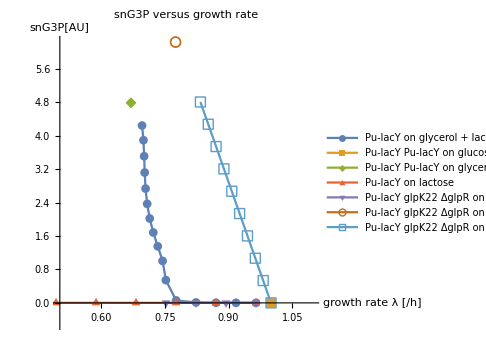

```mathematica
ListPlot[
{
(* Pu-lacY on lactose/glucose and glycerol *)
MakeTableG3PvsGR[5, jmax, 2, j05, kK, kD, nK,nD, h0, νK, m, jGmax, 2], 
(* Pu-lacY on glucose only *)
MakeTableG3PvsGRNG[jmax, jmax,4, j05, kK, kD, nK,nD, h0, νK, 2],
(* Pu-lacY on glycerol only *)
MakeTableG3PvsGR[0, 0, 2, j05, kK, kD, nK,nD, h0, νK, m, jGmax, 2], 
(* Pu-LacY strain on lactose only *)
MakeTableG3PvsGRNG[7, jmax,4,j05, kK, kD, nK,nD, h0, νK, 2], 
(* glpK22 ΔglpR strain on lactose only *)
MakeTableG3PvsGRNG[26, jmax , 3, Infinity, 0,0, nK, nD,  1, νK,2], 
(* glpK22 ΔglpR strain on glycerol only *)
MakeTableG3PvsGR[0, 0, 2, Infinity, 0, 0, nK, nD,  1, νK, m, jGmax, 2], 
 (* glpK22 ΔglpR strain on lactose + glycerol *)
MakeTableG3PvsGR[jmax - 3*Floor[(jmax-7)/3], jmax,3, Infinity,0, 0, nK, nD, 1, νK, m, jGmax, 2]
},
PlotRange->{{0.5,1.1},{-.5,All}},
Joined->True,
AspectRatio->1,
AxesLabel->{
"growth rate λ [/h]",
"snG3P[AU]"
},
PlotLabel->"snG3P versus growth rate",
PlotStyle->AbsolutePointSize[30],
ImageSize->Medium,
PlotMarkers->Automatic,
PlotLegends->{"Pu-lacY on glycerol + lactose", "Pu-lacY Pu-lacY on glucose", "Pu-lacY Pu-lacY on glycerol", "Pu-lacY on lactose", "Pu-lacY glpK22 ΔglpR on lactose only", "Pu-lacY glpK22 ΔglpR on glycerol only", "Pu-lacY glpK22 ΔglpR on lactose + glycerol"}
]
```

### glpFKp expression as a function of growth rate

The model as such cannot predict the expression levels in absolute units.  We therefore normalize all results such that the expression during growth on glycerol only is 2, similar to the measured expression in (again arbitrary) measurement units.

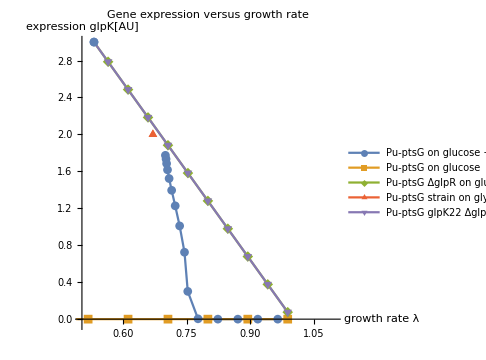

```mathematica
solDK = solveSystemP[0, j05, kK, kD, nK,nD, h0, νK,m, jGmax, 2]; (* glycerol only  *)
glpKlevelGlycerolOnly = 2;
normK = gK[s/.solDK, kK, nK]*fK[λ/.solDK,λC]/glpKlevelGlycerolOnly; (* norm for glpK expression *)
ListPlot[
{
(* Pu-ptsG strain on glucose + glycerol *)
MakeTableGlpKvsGR[7, jmax, 2, j05, kK, kD, nK,nD, h0, νK,m, jGmax, 2, normK],
(* Pu-ptsG strain on glucose *)
MakeTableGlpKvsGRNG[8, jmax, 4, j05, kK, kD, nK,nD, h0, νK, 0,2, normK],(* ΔglpR strain on glucose *)
MakeTableGlpKvsGRNG[8, jmax, 2, j05, 0, 0, nK,nD, h0, νK, 0,2, normK],(* Pu-ptsG strain on glycerol *) 
MakeTableGlpKvsGR[0, 0, 2, j05, kK, kD, nK,nD, h0, νK, m, jGmax, 2, normK], (* glpK22 ΔglpR strain on glucose *)
MakeTableGlpKvsGRNG[8, jmax, 2, Infinity, 0, 0, nK,nD, h0, νK, 0,2, normK] 
}, 
PlotRange->{{0.5,1.1λC},{-.05, 3}}, 
Joined->True,
AspectRatio->1,
AxesLabel->{
HoldForm["growth rate λ"],
HoldForm["expression glpK[AU]"]
},
PlotLabel->HoldForm["Gene expression versus growth rate"],
PlotStyle->AbsolutePointSize[30],
ImageSize->Medium,
PlotMarkers->Automatic,
PlotLegends->{"Pu-ptsG on glucose + glycerol","Pu-ptsG on glucose", "Pu-ptsG ΔglpR on glucose", "Pu-ptsG strain on glycerol", "Pu-ptsG glpK22 ΔglpR on glucose"}
]
```

### glpDp expression as a function of growth rate

Again, we normalize the expression level, this time such that the expression level on glycerol only is 6, similarly to the (also arbitrary) measurement units.

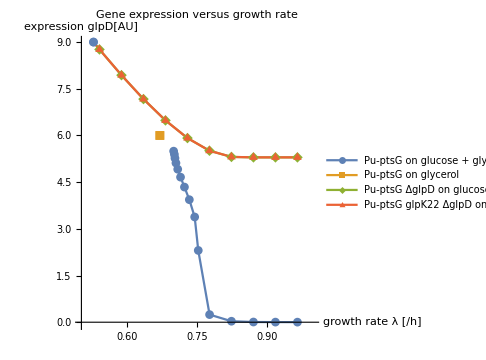

```mathematica
glpDlevelGlycerolOnly = 6;
normD =gD[s/.solDK, kD, nD]*fD[λ/.solDK, Δv, sv, sh, Δh]/glpDlevelGlycerolOnly;
ListPlot[
{
(* Pu-ptsG on glucose + glycerol *)
MakeTableGlpDvsGR[7, jmax, 2, j05, kK, kD, nK,nD, h0, νK,m, jGmax, 2, normD],
(* Pu-ptsG strain on glycerol only *)
MakeTableGlpDvsGR[0, 0, 2, j05, kK, kD, nK,nD, h0, νK, m, jGmax, 2, normD],
(* ΔglpD on glucose *)
MakeTableGlpDvsGRNG[7, jmax, 2, j05, 0, 0, nK,nD, h0, νK,  0,2, normD],(* glpK22 ΔglpD on glucose *)
MakeTableGlpDvsGRNG[7, jmax, 2, Infinity, 0, 0, nK,nD, h0, νK,0,  2, normD]
}, 
PlotRange->{{0.5,λC},{-.05, 9}}, 
Joined-> True,
AspectRatio->1,
AxesLabel->{
HoldForm["growth rate λ [/h]"],
HoldForm["expression glpD[AU]"]
},
PlotLabel->HoldForm["Gene expression versus growth rate"],
PlotStyle->AbsolutePointSize[30],
ImageSize->Medium,
PlotMarkers->Automatic,
PlotLegends->{"Pu-ptsG on glucose + glycerol", "Pu-ptsG on glycerol", "Pu-ptsG ΔglpD on glucose", "Pu-ptsG glpK22 ΔglpD on glucose"}
]
```